# NNListLinePlotMean Tests

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

( last updated:  Tue 11 Mar 2014 11:45:12 )

( current Git HEAD:  38d18b6f1b9d7c4d8adc19783ea68543ebbeac24 )

( http://github.org/ktakagaki/nounoum )

<<Set JLink` java stack size to 6144Mb>>

```mathematica
testData = 
Table[
Table[Sin[x* 2 Pi]+RandomReal[{-1,1}], {x,0,1.5,0.01}],
{30}];
```

```mathematica
Options[NNListLinePlotMean]
```

{NNTracePlot→True,NNMeanPlot→True,NNMeanPlotStyle→{Opacity[0.5,GrayLevel[0]]},NNErrorPlot→True,NNErrorType→StandardError,NNErrorPlotStyle→Opacity[0.25,RGBColor[0,0,1]],NNErrorPlotShaded→True,NNErrorPlotFillingStyle→Opacity[0.25,RGBColor[0,0,1]],PlotStyle→Opacity[0.05,GrayLevel[0]],AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

## You can plot either the standard error (default) or the standard deviation

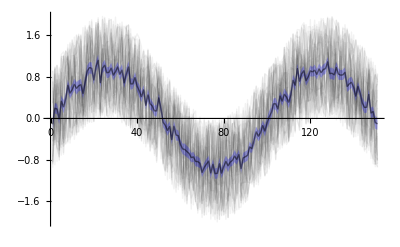

```mathematica
NNListLinePlotMean[ testData,NNErrorPlot->False, NNErrorType->"StandardError" ]
```

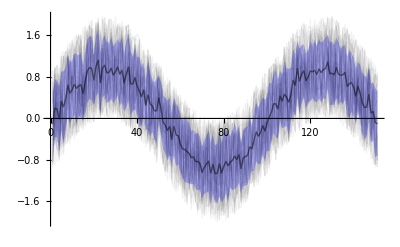

```mathematica
NNListLinePlotMean[ testData,NNErrorPlot->False, NNErrorType->"StandardDeviation" ]
```

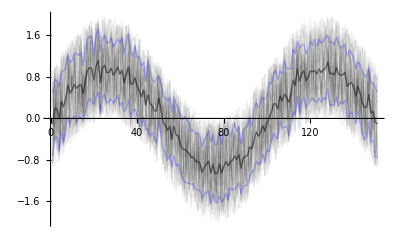

```mathematica
NNListLinePlotMean[ testData,NNErrorPlot->True, NNErrorPlotShaded->False, NNErrorType->"StandardDeviation" ]
```